## The Laplace Transform and Applications Section 6.4 Example

y[t]+y''[t]==ⅇ^t

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/2 (-Cos[t]+ⅇ^t Cos[t]^2-Sin[t]+ⅇ^t Sin[t]^2)]}}

{{y→Function[{t},1/2 (-Cos[t]+ⅇ^t Cos[t]^2-Sin[t]+ⅇ^t Sin[t]^2)]}}

True

0

0

{1/2 (-Cos[t]+ⅇ^t Cos[t]^2-Sin[t]+ⅇ^t Sin[t]^2)}

{1/2 (ⅇ^t-Cos[t]-Sin[t])}

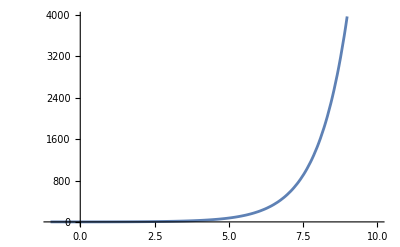

\left\{\frac{1}{2} \left(e^t-\sin (t)-\cos (t)\right)\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+ y[t]==Exp[t]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,10}]
```

```mathematica
Convolve[Sin[x]*HeavisideTheta[x], Exp[x]*HeavisideTheta[x], x, t]
TeXForm[%]
```

-1/2 HeavisideTheta[t] (-ⅇ^t+Cos[t]+Sin[t])

-\frac{1}{2} \theta (t) \left(-e^t+\sin (t)+\cos (t)\right)

## Exercises 1. (i)

π

Cos[t] (-HeavisideTheta[-11 π+t]+HeavisideTheta[-10 π+t])-Cos[t] (-HeavisideTheta[-10 π+t]+HeavisideTheta[-9 π+t])+Cos[t] (-HeavisideTheta[-9 π+t]+HeavisideTheta[-8 π+t])-Cos[t] (-HeavisideTheta[-8 π+t]+HeavisideTheta[-7 π+t])+Cos[t] (-HeavisideTheta[-7 π+t]+HeavisideTheta[-6 π+t])-Cos[t] (-HeavisideTheta[-6 π+t]+HeavisideTheta[-5 π+t])+Cos[t] (-HeavisideTheta[-5 π+t]+HeavisideTheta[-4 π+t])-Cos[t] (-HeavisideTheta[-4 π+t]+HeavisideTheta[-3 π+t])+Cos[t] (-HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t])+Cos[t] (HeavisideTheta[t]-HeavisideTheta[-π+t])-Cos[t] (-HeavisideTheta[-2 π+t]+HeavisideTheta[-π+t])

Cos[t] (HeavisideTheta[t]-HeavisideTheta[-11 π+t]+2 (HeavisideTheta[-10 π+t]-HeavisideTheta[-9 π+t]+HeavisideTheta[-8 π+t]-HeavisideTheta[-7 π+t]+HeavisideTheta[-6 π+t]-HeavisideTheta[-5 π+t]+HeavisideTheta[-4 π+t]-HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]))

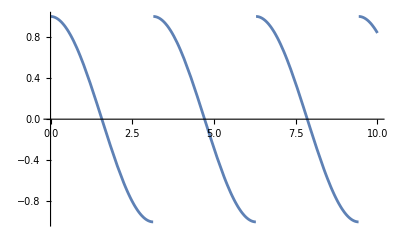

((1+ⅇ^(-π s)) s)/((1-ⅇ^(-π s)) (1+s^2))

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-1.pdf

\frac{\left(e^{-\pi  s}+1\right) s}{\left(1-e^{-\pi  s}\right) \left(s^2+1\right)}

```mathematica
f[t_]:=Cos[t]
T=Pi
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
Simplify[%]
plot741=Plot[g[t], {t, 0, 10}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-1.pdf",plot741]
```

## 1(ii)

3

(-30+t) (-HeavisideTheta[-33+t]+HeavisideTheta[-30+t])+(-27+t) (-HeavisideTheta[-30+t]+HeavisideTheta[-27+t])+(-24+t) (-HeavisideTheta[-27+t]+HeavisideTheta[-24+t])+(-21+t) (-HeavisideTheta[-24+t]+HeavisideTheta[-21+t])+(-18+t) (-HeavisideTheta[-21+t]+HeavisideTheta[-18+t])+(-15+t) (-HeavisideTheta[-18+t]+HeavisideTheta[-15+t])+(-12+t) (-HeavisideTheta[-15+t]+HeavisideTheta[-12+t])+(-9+t) (-HeavisideTheta[-12+t]+HeavisideTheta[-9+t])+(-6+t) (-HeavisideTheta[-9+t]+HeavisideTheta[-6+t])+(-3+t) (-HeavisideTheta[-6+t]+HeavisideTheta[-3+t])+t (-HeavisideTheta[-3+t]+HeavisideTheta[t])

-((-30+t) HeavisideTheta[-33+t])-3 HeavisideTheta[-30+t]-3 HeavisideTheta[-27+t]-3 HeavisideTheta[-24+t]-3 HeavisideTheta[-21+t]-3 HeavisideTheta[-18+t]-3 HeavisideTheta[-15+t]-3 HeavisideTheta[-12+t]-3 HeavisideTheta[-9+t]-3 HeavisideTheta[-6+t]-3 HeavisideTheta[-3+t]+t HeavisideTheta[t]

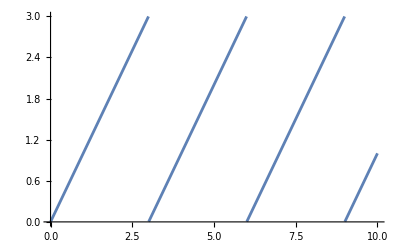

(1-ⅇ^(-3 s) (1+3 s))/((1-ⅇ^(-3 s)) s^2)

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-2.pdf

\frac{1-e^{-3 s} (3 s+1)}{\left(1-e^{-3 s}\right) s^2}

```mathematica
f[t_]:=t
T=3
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
Simplify[%]
plot742=Plot[g[t], {t, 0, 10}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-2.pdf",plot742]
```

## 1(iii)

4

(-42+t) (-HeavisideTheta[-44+t]+HeavisideTheta[-40+t])+(-38+t) (-HeavisideTheta[-40+t]+HeavisideTheta[-36+t])+(-34+t) (-HeavisideTheta[-36+t]+HeavisideTheta[-32+t])+(-30+t) (-HeavisideTheta[-32+t]+HeavisideTheta[-28+t])+(-26+t) (-HeavisideTheta[-28+t]+HeavisideTheta[-24+t])+(-22+t) (-HeavisideTheta[-24+t]+HeavisideTheta[-20+t])+(-18+t) (-HeavisideTheta[-20+t]+HeavisideTheta[-16+t])+(-14+t) (-HeavisideTheta[-16+t]+HeavisideTheta[-12+t])+(-10+t) (-HeavisideTheta[-12+t]+HeavisideTheta[-8+t])+(-6+t) (-HeavisideTheta[-8+t]+HeavisideTheta[-4+t])+(-2+t) (-HeavisideTheta[-4+t]+HeavisideTheta[t])

-((-42+t) HeavisideTheta[-44+t])-4 HeavisideTheta[-40+t]-4 HeavisideTheta[-36+t]-4 HeavisideTheta[-32+t]-4 HeavisideTheta[-28+t]-4 HeavisideTheta[-24+t]-4 HeavisideTheta[-20+t]-4 HeavisideTheta[-16+t]-4 HeavisideTheta[-12+t]-4 HeavisideTheta[-8+t]-4 HeavisideTheta[-4+t]-2 HeavisideTheta[t]+t HeavisideTheta[t]

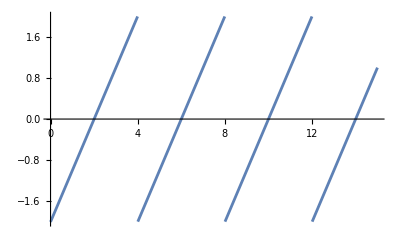

(1-2 s-ⅇ^(-4 s) (1+2 s))/((1-ⅇ^(-4 s)) s^2)

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-3.pdf

\frac{-2 s-e^{-4 s} (2 s+1)+1}{\left(1-e^{-4 s}\right) s^2}

```mathematica
f[t_]:=t-2
T=4
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
Simplify[%]
plot743=Plot[g[t], {t, 0, 15}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-3.pdf",plot743]
```

## 1(iv)

2

(-HeavisideTheta[-22+t]+HeavisideTheta[-20+t]) (-HeavisideTheta[-21+t]+HeavisideTheta[-20+t])+(-HeavisideTheta[-20+t]+HeavisideTheta[-18+t]) (-HeavisideTheta[-19+t]+HeavisideTheta[-18+t])+(-HeavisideTheta[-18+t]+HeavisideTheta[-16+t]) (-HeavisideTheta[-17+t]+HeavisideTheta[-16+t])+(-HeavisideTheta[-16+t]+HeavisideTheta[-14+t]) (-HeavisideTheta[-15+t]+HeavisideTheta[-14+t])+(-HeavisideTheta[-14+t]+HeavisideTheta[-12+t]) (-HeavisideTheta[-13+t]+HeavisideTheta[-12+t])+(-HeavisideTheta[-12+t]+HeavisideTheta[-10+t]) (-HeavisideTheta[-11+t]+HeavisideTheta[-10+t])+(-HeavisideTheta[-10+t]+HeavisideTheta[-8+t]) (-HeavisideTheta[-9+t]+HeavisideTheta[-8+t])+(-HeavisideTheta[-8+t]+HeavisideTheta[-6+t]) (-HeavisideTheta[-7+t]+HeavisideTheta[-6+t])+(-HeavisideTheta[-6+t]+HeavisideTheta[-4+t]) (-HeavisideTheta[-5+t]+HeavisideTheta[-4+t])+(-HeavisideTheta[-4+t]+HeavisideTheta[-2+t]) (-HeavisideTheta[-3+t]+HeavisideTheta[-2+t])+(-HeavisideTheta[-2+t]+HeavisideTheta[t]) (-HeavisideTheta[-1+t]+HeavisideTheta[t])

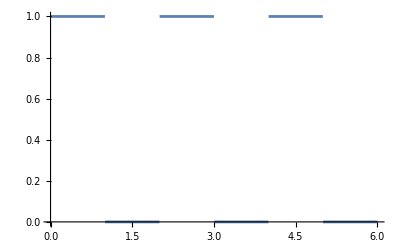

(1-ⅇ^-s)/((1-ⅇ^(-2 s)) s)

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-4.pdf

\frac{1-e^{-s}}{\left(1-e^{-2 s}\right) s}

```mathematica
f[t_]:=HeavisideTheta[t]-HeavisideTheta[t-1]
T=2
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
(*Evaluate[%]*)
plot744=Plot[g[t], {t, 0, 6}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-4.pdf",plot744]
```

## 1(v)

2 π

(-HeavisideTheta[-22 π+t]+HeavisideTheta[-20 π+t]) (-HeavisideTheta[-21 π+t]+HeavisideTheta[-20 π+t]) Sin[t]+(-HeavisideTheta[-20 π+t]+HeavisideTheta[-18 π+t]) (-HeavisideTheta[-19 π+t]+HeavisideTheta[-18 π+t]) Sin[t]+(-HeavisideTheta[-18 π+t]+HeavisideTheta[-16 π+t]) (-HeavisideTheta[-17 π+t]+HeavisideTheta[-16 π+t]) Sin[t]+(-HeavisideTheta[-16 π+t]+HeavisideTheta[-14 π+t]) (-HeavisideTheta[-15 π+t]+HeavisideTheta[-14 π+t]) Sin[t]+(-HeavisideTheta[-14 π+t]+HeavisideTheta[-12 π+t]) (-HeavisideTheta[-13 π+t]+HeavisideTheta[-12 π+t]) Sin[t]+(-HeavisideTheta[-12 π+t]+HeavisideTheta[-10 π+t]) (-HeavisideTheta[-11 π+t]+HeavisideTheta[-10 π+t]) Sin[t]+(-HeavisideTheta[-10 π+t]+HeavisideTheta[-8 π+t]) (-HeavisideTheta[-9 π+t]+HeavisideTheta[-8 π+t]) Sin[t]+(-HeavisideTheta[-8 π+t]+HeavisideTheta[-6 π+t]) (-HeavisideTheta[-7 π+t]+HeavisideTheta[-6 π+t]) Sin[t]+(-HeavisideTheta[-6 π+t]+HeavisideTheta[-4 π+t]) (-HeavisideTheta[-5 π+t]+HeavisideTheta[-4 π+t]) Sin[t]+(-HeavisideTheta[-4 π+t]+HeavisideTheta[-2 π+t]) (-HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t]) Sin[t]+(HeavisideTheta[t]-HeavisideTheta[-2 π+t]) (HeavisideTheta[t]-HeavisideTheta[-π+t]) Sin[t]

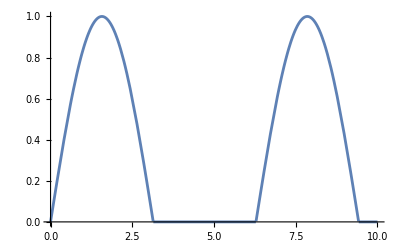

(1+ⅇ^(-π s))/((1-ⅇ^(-2 π s)) (1+s^2))

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-5.pdf

\frac{e^{-\pi  s}+1}{\left(1-e^{-2 \pi  s}\right) \left(s^2+1\right)}

```mathematica
f[t_]:=Sin[t]*(HeavisideTheta[t]-HeavisideTheta[t-Pi])
T=2*Pi
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
(*Evaluate[%]*)
plot745=Plot[g[t], {t, 0, 10}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-5.pdf",plot745]
```

## 1(vi)

2 π

ⅇ^(-2 (-20 π+t)) (-HeavisideTheta[-22 π+t]+HeavisideTheta[-20 π+t]) (-HeavisideTheta[-21 π+t]+HeavisideTheta[-20 π+t]) Sin[t]+ⅇ^(-2 (-18 π+t)) (-HeavisideTheta[-20 π+t]+HeavisideTheta[-18 π+t]) (-HeavisideTheta[-19 π+t]+HeavisideTheta[-18 π+t]) Sin[t]+ⅇ^(-2 (-16 π+t)) (-HeavisideTheta[-18 π+t]+HeavisideTheta[-16 π+t]) (-HeavisideTheta[-17 π+t]+HeavisideTheta[-16 π+t]) Sin[t]+ⅇ^(-2 (-14 π+t)) (-HeavisideTheta[-16 π+t]+HeavisideTheta[-14 π+t]) (-HeavisideTheta[-15 π+t]+HeavisideTheta[-14 π+t]) Sin[t]+ⅇ^(-2 (-12 π+t)) (-HeavisideTheta[-14 π+t]+HeavisideTheta[-12 π+t]) (-HeavisideTheta[-13 π+t]+HeavisideTheta[-12 π+t]) Sin[t]+ⅇ^(-2 (-10 π+t)) (-HeavisideTheta[-12 π+t]+HeavisideTheta[-10 π+t]) (-HeavisideTheta[-11 π+t]+HeavisideTheta[-10 π+t]) Sin[t]+ⅇ^(-2 (-8 π+t)) (-HeavisideTheta[-10 π+t]+HeavisideTheta[-8 π+t]) (-HeavisideTheta[-9 π+t]+HeavisideTheta[-8 π+t]) Sin[t]+ⅇ^(-2 (-6 π+t)) (-HeavisideTheta[-8 π+t]+HeavisideTheta[-6 π+t]) (-HeavisideTheta[-7 π+t]+HeavisideTheta[-6 π+t]) Sin[t]+ⅇ^(-2 (-4 π+t)) (-HeavisideTheta[-6 π+t]+HeavisideTheta[-4 π+t]) (-HeavisideTheta[-5 π+t]+HeavisideTheta[-4 π+t]) Sin[t]+ⅇ^(-2 (-2 π+t)) (-HeavisideTheta[-4 π+t]+HeavisideTheta[-2 π+t]) (-HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t]) Sin[t]+ⅇ^(-2 t) (HeavisideTheta[t]-HeavisideTheta[-2 π+t]) (HeavisideTheta[t]-HeavisideTheta[-π+t]) Sin[t]

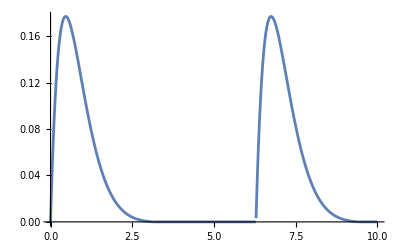

(1+ⅇ^(-π (2+s)))/((1-ⅇ^(-2 π s)) (5+4 s+s^2))

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap07/Mathematica

7-4-6.pdf

\frac{e^{-\pi  (s+2)}+1}{\left(1-e^{-2 \pi  s}\right) \left(s^2+4 s+5\right)}

```mathematica
f[t_]:=Exp[-2t]*Sin[t]*(HeavisideTheta[t]-HeavisideTheta[t-Pi])
T=2*Pi
g[t_]:= Sum[f[t-k*T]*(HeavisideTheta[t-k*T]- HeavisideTheta[t-(k+1)*T]),{k,0, 10}]
g[t]
(*Evaluate[%]*)
plot746=Plot[g[t], {t, 0, 10}]
laplacetransform=(1/(1-Exp[-T*s]))*Integrate[f[t]*Exp[-s*t],  {t, 0, T}]
TeXForm[%]
SetDirectory[NotebookDirectory[]]
Export["7-4-6.pdf",plot746]
```

## 2 (i) , for for

Piecewise[{{0, 0≤Mod[t,2]≤1}, {1, 1≤Mod[t,2]<2}, {0, True}}]

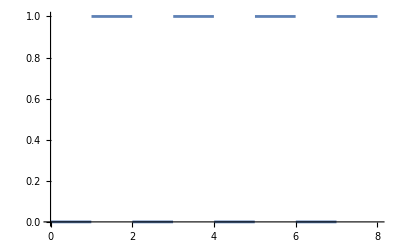

0

1/(s+ⅇ^s s)

1/(3 s)-1/(2 (1+s))+1/(6 (3+s))

```mathematica
period=2;  (*Define the period*)
f[t_]:=Piecewise[{{0, 0<=t<=1},{1, 1<=t<2}}]; (*Define your function*)
p[t_]:=f[Mod[t,period]];
p[t]
Plot[p[t],{t,0,4*period}]
p[5]
F[s_]:=LaplaceTransform[p[t], t, s]
F[s]
Apart[1/(s(s+1)(s+3))]
```

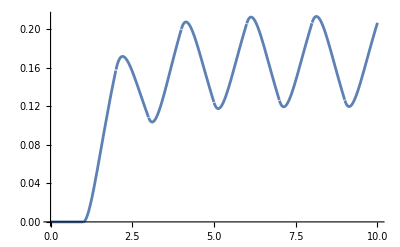

```mathematica
y[t_]:= Sum[(-1)^{(n+1)}*UnitStep[t-n]*(1/3-Exp[-(t-n)]/2+Exp[-3(t-n)]/6), {n, 1, 100}];
y[t];
Plot[y[t], {t, 0, 10}]
```

1/2 Convolve[(Piecewise[{{0, 0≤Mod[t,2]≤1}, {1, 1≤Mod[t,2]<2}, {0, True}}]) UnitStep[t],(-ⅇ^(-3 t)+ⅇ^-t) UnitStep[t],t,x]

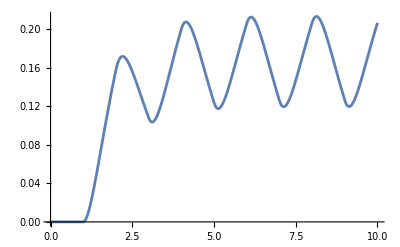

```mathematica
h[t_]:=1/2(Exp[-t]-Exp[-3t])
k[x_]:= Convolve[p[t]*UnitStep[t],h[t]*UnitStep[t],t,x]
k[x]
plot741=Plot[k[x], {x, 0, 10}]
```

## 2(ii)

Piecewise[{{1, 0≤Mod[t,2]≤1}, {-1, 1≤Mod[t,2]<2}, {0, True}}]

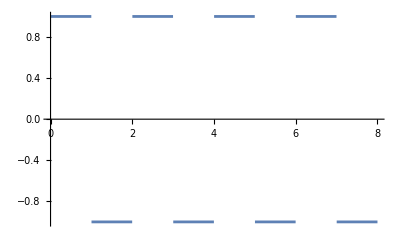

1

Tanh[s/2]/s

-1/(4 s)+1/(2 (2+s)^2)+1/(4 (2+s))

-1/4+ⅇ^(-2 t)/4+1/2 ⅇ^(-2 t) t

1/(2 s)-1/(2+s)^2-1/(2 (2+s))

1/2-ⅇ^(-2 t)/2-ⅇ^(-2 t) t

ⅇ^(-2 t) t

```mathematica
period=2;  (*Define the period*)
f[t_]:=Piecewise[{{1, 0<=t<=1},{-1, 1<=t<2}}]; (*Define your function*)
p[t_]:=f[Mod[t,period]];
p[t]
Plot[p[t],{t,0,4*period}]
p[5]
LaplaceTransform[p[t], t, s]
Apart[-1/(s(s+2)^2)]
Distribute[InverseLaplaceTransform[%, s, t]]
Apart[2/(s(s+2)^2)]
Distribute[InverseLaplaceTransform[%, s, t]]
InverseLaplaceTransform[1/((s+2)^2), s, t]
```

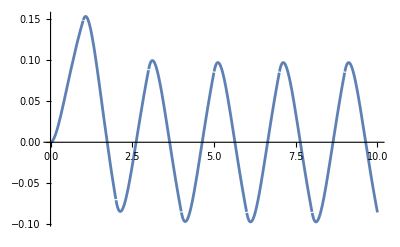

```mathematica
y[t_]:= (1/2)*t*Exp[-2t]+(1/4)*Exp[-2t]-1/4+Sum[(-1)^{n}*UnitStep[t-n]*(1/2-Exp[-2(t-n)]/2-(t-n)*Exp[-2(t-n)]), {n, 0, 100}];
y[t];
Plot[y[t], {t, 0, 10}]
```

Convolve[(Piecewise[{{1, 0≤Mod[t,2]≤1}, {-1, 1≤Mod[t,2]<2}, {0, True}}]) UnitStep[t],ⅇ^(-2 t) t UnitStep[t],t,x]

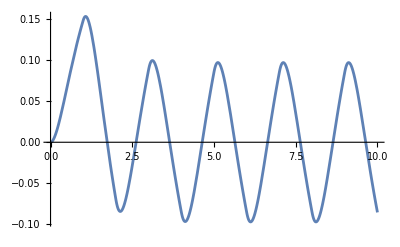

```mathematica
h[t_]:=t*Exp[-2t]
k[x_]:= Convolve[p[t]*UnitStep[t],h[t]*UnitStep[t],t,x]
k[x]
plot741=Plot[k[x], {x, 0, 10}]
```

## 2 (iii)

Piecewise[{{Sin[Mod[t,2 π]], 0≤Mod[t,2 π]≤π}, {0, True}}]

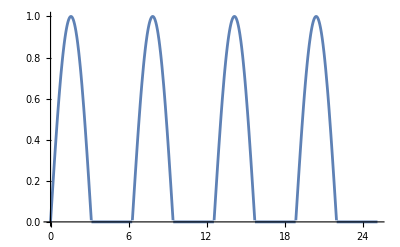

0

1/(1+s^2-ⅇ^(-π s) (1+s^2))

1/(2 (1+s))-1/(5 (2+s))+(1-3 s)/(10 (1+s^2))

1/10 (ⅇ^(-2 t) (-2+5 ⅇ^t)-3 Cos[t]+Sin[t])

1/10 ⅇ^(-2 t) (-2+5 ⅇ^t)-(3 Cos[t])/10+Sin[t]/10

ⅇ^(-2 t) (-1+ⅇ^t)

```mathematica
period=2Pi;  (*Define the period*)
f[t_]:=Piecewise[{{Sin[t], 0<=t<=Pi},{0, Pi<=t<2Pi}}]; ; (*Define your function*)
p[t_]:=f[Mod[t,period]];
p[t]
Plot[p[t],{t,0,4*period}]
p[5]
LaplaceTransform[p[t], t, s]
Apart[1/((s+1)(s+2)(s^2+1))]
InverseLaplaceTransform[%, s, t]
Distribute[%]
InverseLaplaceTransform[1/((s+1)(s+2)), s, t]
```

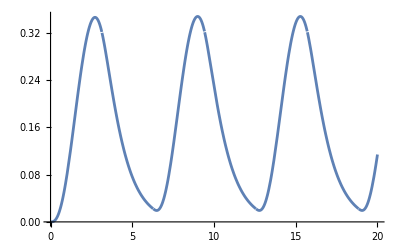

```mathematica
y[t_]:= (1/10)*Sum[UnitStep[t-n*Pi]* (Sin[t-n*Pi]-3*Cos[t-n*Pi]+5Exp[-(t-n*Pi)]-2*Exp[-2(t-n*Pi)]), {n, 0, 200}];
y[t];
Plot[y[t], {t, 0, 20}]
```

Convolve[(Piecewise[{{Sin[Mod[t,2 π]], 0≤Mod[t,2 π]≤π}, {0, True}}]) UnitStep[t],(-ⅇ^(-2 t)+ⅇ^-t) UnitStep[t],t,x]

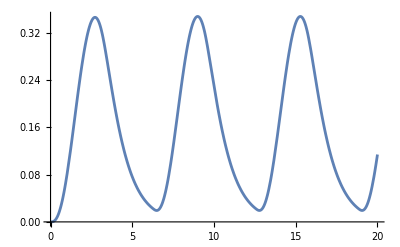

```mathematica
h[t_]:=Exp[-t]-Exp[-2t]
k[x_]:= Convolve[p[t]*UnitStep[t],h[t]*UnitStep[t],t,x]
k[x]
plot741=Plot[k[x], {x, 0, 20}]
```

## 2 (iv)

Mod[t,3]

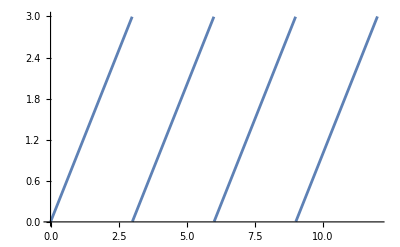

2

1/(s^2+(3 s^3)/(-1+ⅇ^(3 s)-3 s))

1/(4 s^2)-1/(4 (4+s^2))

t/4-1/4 Cos[t] Sin[t]

3/(4 s)-(3 s)/(4 (4+s^2))

(3 Sin[t]^2)/2

```mathematica
period=3;  (*Define the period*)
f[t_]:=t; (*Define your function*)
p[t_]:=f[Mod[t,period]];
p[t]
Plot[p[t],{t,0,4*period}]
p[5]
LaplaceTransform[p[t], t, s]
Apart[1/(s^2(s^2+4))]
Distribute[InverseLaplaceTransform[%, s, t]]
Apart[3/(s(s^2+4))]
Distribute[InverseLaplaceTransform[%, s, t]]
```

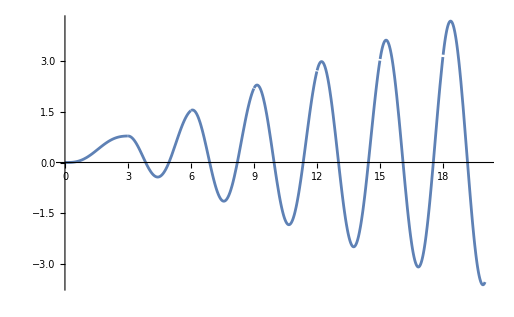

```mathematica
y[t_]:= (1/4)*(t- Sin[t] * Cos[t])-(3/2)*Sum[UnitStep[t-3n]* (Sin[t-3n])^2, {n, 1, 100}];
y[t];
Plot[y[t], {t, 0, 20}]
```

```mathematica
h[t_]:=Cos[t]*Sin[t]
k[x_]:= Convolve[p[t]*UnitStep[t],h[t]*UnitStep[t],t,x]
k[x]
plot741=Plot[k[x], {x, 0, 20}]
```

Convolve[Mod[t,3] UnitStep[t],Cos[t] Sin[t] UnitStep[t],t,x]